```mathematica
PhiData=Catenate@Table[Import[FileNameJoin[{NotebookDirectory[],"data","all_phi","Phi_"<>name<>".csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ
,{name,{"0_1000","1000_2000","2000_3000","3000_4000","4000_5000","5000_6000","6000_7000","7000_8000","8000_9000","9000_10080"}}];
SensitivityData=Import[FileNameJoin[{NotebookDirectory[],"data","sensitivity.csv"}]]⟦2;;⟧ᵀ⟦2;;⟧ᵀ;
```

```mathematica
Length[PhiData]
```

10080

```mathematica
PhiData⟦1⟧
```

{0.1875,0.1875,2.3125,0.687499,0.1875,0.1875}

```mathematica
Length[SensitivityData]
```

10080

```mathematica
SΦ=Table[{Mean[SensitivityData⟦i⟧],Mean[PhiData⟦i⟧]},{i,1,Length[PhiData]}];
```

```mathematica
ListPlot[SΦ]
```

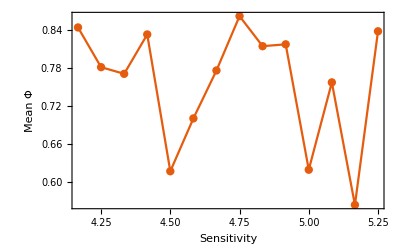

```mathematica
ListLinePlot[SortBy[Mean/@GatherBy[SΦ,First],First],PlotRange->All,Mesh->Full,PlotTheme->"Scientific",FrameLabel->{"Sensitivity","Mean Φ"}]
```

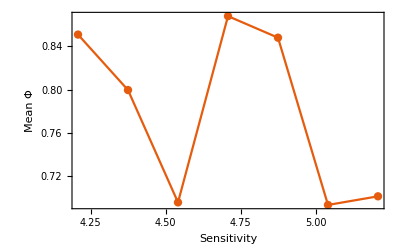

```mathematica
ListLinePlot[(Median/@Partition[#,2])&@SortBy[Median/@GatherBy[SΦ,First],First],PlotRange->All,Mesh->Full,PlotTheme->"Scientific",FrameLabel->{"Sensitivity","Mean Φ"}]
```

```mathematica
SortBy[Mean/@GatherBy[SΦ,First],First]
```

{{25/6,0.844166},{17/4,0.781396},{13/3,0.770866},{53/12,0.833074},{9/2,0.616889},{55/12,0.700418},{14/3,0.776149},{19/4,0.86205},{29/6,0.814551},{59/12,0.817494},{5,0.61932},{61/12,0.75735},{31/6,0.563659},{21/4,0.838112}}

```mathematica
{S,Φs}=SortBy[{#⟦1,1⟧,#ᵀ⟦2⟧}&/@GatherBy[SΦ,First],First]ᵀ;
```

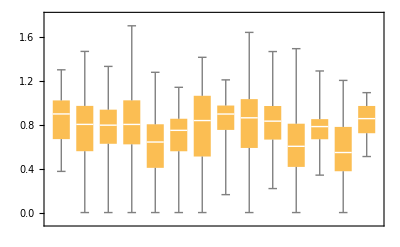

```mathematica
BoxWhiskerChart[Φs]
```